```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

## Analytical comparison of volume perturbations

Using DSolve, we find the following expressions for the volume perturbations in GR in GFT:

```mathematica
Subscript[δV, GFT][x_,k_,H_]:=Subscript[c, 1,GFT]*4 ⅇ^(-(3 H x)/2) BesselJ[-3/4,(√(ⅇ^(4 H x) k^2))/(2 H)]  Gamma[5/4]+Subscript[c, 2,GFT]*ⅇ^(-(3 H x)/2) BesselJ[3/4,(√(ⅇ^(4 H x) k^2))/(2 H)] C[2] Gamma[7/4]
Subscript[δV, GR][x_,k_,H_]:=Subscript[c, 1,GR]*BesselJ[0,(√(ⅇ^(4 H x)) k)/(2 H)] +Subscript[c, 2,GR]*2 BesselY[0,(√(ⅇ^(4 H x)) k)/(2 H)]
```

Notice, that here, δV refers to the ratio of the volume perturbations and the background volume. 
In the following, we consider a matching of initial conditions for super-, intermediate and sub-horizon modes.
For time t_today at arbitrary value, we find:

```mathematica
DSolve[Subscript[δV, GR]''[x]+Exp[4*H*(x-x0)]*k^2*Subscript[δV, GR][x]==0,Subscript[δV, GR][x],x,Assumptions->Element[{x,x0,k,H},Reals]]
DSolve[Subscript[δV, GFT]''[x]+Exp[4*H*(x-x0)]*k^2*Subscript[δV, GFT][x]==-3*H*Subscript[δV, GFT]'[x],Subscript[δV, GFT][x],x,Assumptions->Element[{x0,x,k,H},Reals]]
```

{{δV_GR[x]→BesselJ[0,(ⅇ^(2 H x-2 H x0) k)/(2 H)] C[1]+2 BesselY[0,(ⅇ^(2 H x-2 H x0) k)/(2 H)] C[2]}}

{{δV_GFT[x]→4 ⅇ^(-(3 H x)/2) BesselJ[-3/4,(ⅇ^(2 H x-2 H x0) k)/(2 H)] C[1] Gamma[5/4]+ⅇ^(-(3 H x)/2) BesselJ[3/4,(ⅇ^(2 H x-2 H x0) k)/(2 H)] C[2] Gamma[7/4]}}

```mathematica
D[BesselJ[3/4,x],x]
```

1/2 (BesselJ[-1/4,x]-BesselJ[7/4,x])

### Super-horizon modes

To match the perturbations in the super-horizon limit, i.e. (k/H)<<1, we must set c_(2,GR) = 0 and c_(1,GFT) = 0. Furthermore, matching requires to impose the relation c_(2,GFT) = (H/k)^(3/4)*Γ(7/4)c_(1,GR). For clarity of the k-limits, we introduce κ = k/H.

```mathematica
Subscript[δV, GFT,super][x_,x0_,κ_,H_,c_]:=c*(4/κ)^(3/4)Gamma[7/4] ⅇ^(-(3 H (x-x0))/2) BesselJ[3/4,ⅇ^(2 H(x-x0))/2 κ];
Subscript[δV, GR,super][x_,x0_,κ_,H_,c_]:=c*BesselJ[0,ⅇ^(2 H(x-x0))/2 κ] ;
```

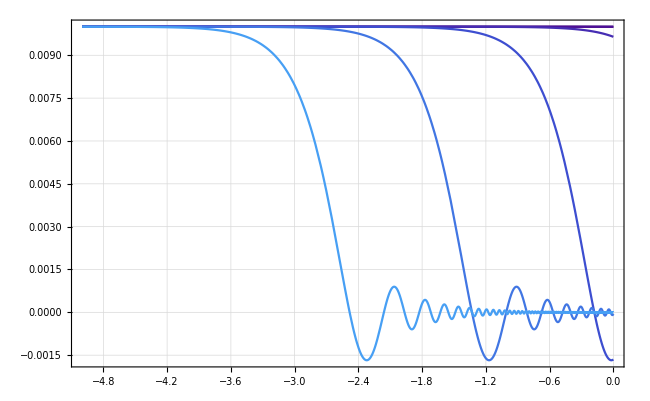

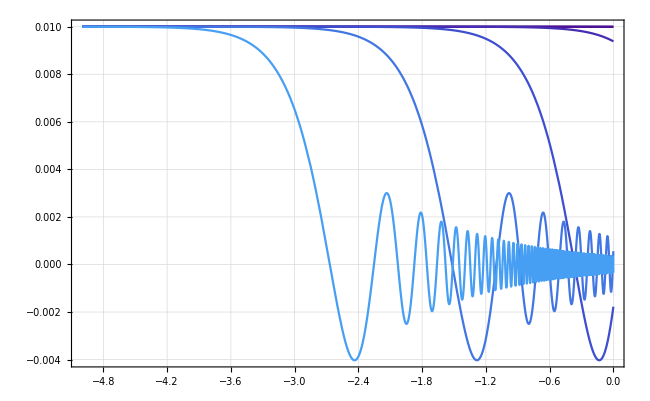

```mathematica
volumepertGFT=Plot[Evaluate@Table[Subscript[δV, GFT,super][x,0,10^(n),1,0.01],{n,-2,3}],{x,-5,0},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\delta V_{\mathrm{GFT}}/\overline{V}",Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72},PlotRange->Full,ImageSize->650,FrameTicksStyle->Directive[FontSize->16]]
volumepertGR=Plot[Evaluate@Table[Subscript[δV, GR,super][x,0,10^(n),1,0.01],{n,-2,3}],{x,-5,0},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\delta V_{\mathrm{GR}}/\overline{V}",Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72},PlotRange->Full,ImageSize->650,FrameTicksStyle->Directive[FontSize->16]]
(*Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/volume_pert_GFT.pdf",volumepertGFT];
Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/volume_pert_GR.pdf",volumepertGR];*)
```

Notice, that different values of H simply correspond to a re-scaling of time.  One could define the variable τ = Ht to define the re-scaled evolution of the perturbations.

### Exact horizon modes

```mathematica
Subscript[δV, GR,trans][τ_,κ_]:=BesselJ[0,(√(ⅇ^(4 τ)))/2 κ]
```

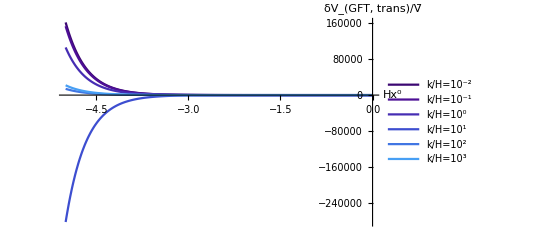

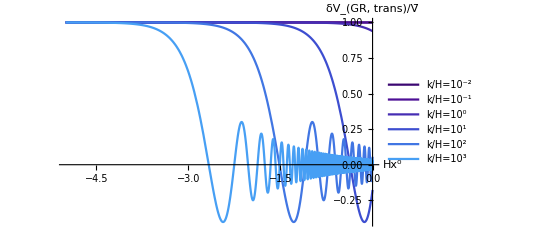

```mathematica
Subscript[δV, GFT,trans][τ_,κ_]:=(BesselJ[0,κ/(2 ⅇ^2)]/ⅇ^(3/2)-BesselJ[3/4,κ/(2 ⅇ^2)] Gamma[7/4])/(4 BesselJ[-3/4,κ/(2 ⅇ^2)] Gamma[5/4])*4 ⅇ^(-(3 τ)/2) BesselJ[-3/4,(√(ⅇ^(4 τ)))/2 κ]  Gamma[5/4]+ⅇ^(-(3 τ)/2) BesselJ[3/4,(√(ⅇ^(4 τ)))/2 κ] Gamma[7/4]
Plot[Evaluate@Table[Subscript[δV, GFT,trans][x,10^(n)],{n,-2,3}],{x,-5,0},PlotLegends->{"k/H=10^-2","k/H=10^-1","k/H=10^0","k/H=10^1","k/H=10^2","k/H=10^3"},AxesLabel->{"Hx^0","δV_(GFT, trans)/V̄"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72},PlotRange->Full]
Plot[Evaluate@Table[Subscript[δV, GR,trans][x,10^(n)],{n,-2,3}],{x,-5,0},PlotLegends->{"k/H=10^-2","k/H=10^-1","k/H=10^0","k/H=10^1","k/H=10^2","k/H=10^3"},AxesLabel->{"Hx^0","δV_(GR, trans)/V̄"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72},PlotRange->Full]
```

```mathematica
Solve[Subscript[c, 1,GFT]*4 ⅇ^(-(3 H x)/2) BesselJ[-3/4,(√(ⅇ^(4 H x) k^2))/(2 H)]  Gamma[5/4]+Subscript[c, 2,GFT]*ⅇ^(-(3 H x)/2) BesselJ[3/4,(√(ⅇ^(4 H x) k^2))/(2 H)] Gamma[7/4]==BesselJ[0,(√(ⅇ^(4 H x)) k)/(2 H)] ,{Subscript[c, 2,GFT],Subscript[c, 1,GFT]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(1,GFT)→(ⅇ^((3 H x)/2) BesselJ[0,(√(ⅇ^(4 H x)) k)/(2 H)])/(4 BesselJ[-3/4,(√(ⅇ^(4 H x) k^2))/(2 H)] Gamma[5/4])-(BesselJ[3/4,(√(ⅇ^(4 H x) k^2))/(2 H)] Gamma[7/4] c_(2,GFT))/(4 BesselJ[-3/4,(√(ⅇ^(4 H x) k^2))/(2 H)] Gamma[5/4])}}

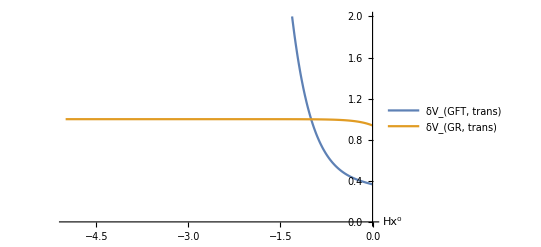

```mathematica
Plot[{Subscript[δV, GFT,trans][x,1],Subscript[δV, GR,trans][x,1]},{x,-5,0},PlotLegends->{"δV_(GFT, trans)", "δV_(GR, trans)"},AxesLabel->{"Hx^0"},PlotRange->{{-5,0},{0,2}}]
```

If one tries to find a matching for Planckian modes at a certain time τ_*, which we chosen here to be -1, then the matching only holds for this point and deviations are strong otherwise. Therefore, a matching of Planckian modes cannot be done consistently for more then exact one instance of time.

### Sub-horizon modes

```mathematica
Solve[a*Cos[x-Pi/8]+b*Cos[x-(5Pi)/8]==Cos[x-Pi/4],{a,b}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→a Cot[π/8-x]-Cos[π/4-x] Csc[π/8-x]}}

Given the asymptotic form of the general solution δV_GR and δV_GFT, one faces the same struggles for matching as for the horizon mode. Thus, a consistent matching that is stable under time evolution is not possible.

## Analytical comparison of matter perturbations

For general modes k, the differential equation for the GR matter perturbations is given by:

```mathematica
DSolve[Subscript[δϕ, GR]''[x]+Exp[4*H*x]*k^2*Subscript[δϕ, GR][x]==0,Subscript[δϕ, GR][x],x]
```

{{δϕ_GR[x]→BesselJ[0,(√(ⅇ^(4 H x)) k)/(2 H)] C[1]+2 BesselY[0,(√(ⅇ^(4 H x)) k)/(2 H)] C[2]}}

with solutions

```mathematica
Subscript[δϕ, GR][x_,κ_,H_]:=BesselJ[0,(√(ⅇ^(4 H x)))/2 κ]
```

For GFT, the geometry enters the right-hand side of the differential equation. Above, we have seen that the best match is obtained by the initial conditions in the super-horizon limit. These are the initial conditions that we use for the geometry. The derivative of δV_(GFT,super) is given by

```mathematica
D[((4H)/k)^(3/4)Gamma[7/4] ⅇ^(-(3 H x)/2) BesselJ[3/4,(√(ⅇ^(4 H x))*k)/(2 H)],x]
```

-3 √2 ⅇ^(-(3 H x)/2) H (H/k)^(3/4) BesselJ[3/4,(√(ⅇ^(4 H x)) k)/(2 H)] Gamma[7/4]+√2 ⅇ^(-(3 H x)/2) √(ⅇ^(4 H x)) (H/k)^(3/4) k (BesselJ[-1/4,(√(ⅇ^(4 H x)) k)/(2 H)]-BesselJ[7/4,(√(ⅇ^(4 H x)) k)/(2 H)]) Gamma[7/4]

Also, we need the background equations

```mathematica
ϕ̄[x_,H_]:=-Sqrt[8/3]+Sqrt[6]*H*x;
OverBar[dϕ][H_]:=Sqrt[6]*H;
DSolve[f''[x]+Exp[4*H*x]*k^2*f[x]==(-3*H*ϕ̄[x,H]+2*OverBar[dϕ][H] )*(-3 √2 ⅇ^(-(3 H x)/2) H (H/k)^(3/4) BesselJ[3/4,(√(ⅇ^(4 H x)) k)/(2 H)] Gamma[7/4]+√2 ⅇ^(-(3 H x)/2) √(ⅇ^(4 H x)) (H/k)^(3/4) k (BesselJ[-1/4,(√(ⅇ^(4 H x)) k)/(2 H)]-BesselJ[7/4,(√(ⅇ^(4 H x)) k)/(2 H)]) Gamma[7/4]),f[x],x]
```

{{f[x]→BesselJ[0,(√(ⅇ^(4 H x)) k)/(2 H)] C[1]+2 BesselY[0,(√(ⅇ^(4 H x)) k)/(2 H)] C[2]+BesselJ[0,(√(ⅇ^(4 H x)) k)/(2 H)] (-2 √3 ⅇ^(-3/2 H K[1]) √(ⅇ^(4 H K[1])) (H/k)^(3/4) k π BesselJ[-1/4,(√(ⅇ^(4 H K[1])) k)/(2 H)] BesselY[0,(√(ⅇ^(4 H K[1])) k)/(2 H)] Gamma[7/4]+6 √3 ⅇ^(-3/2 H K[1]) H (H/k)^(3/4) π BesselJ[3/4,(√(ⅇ^(4 H K[1])) k)/(2 H)] BesselY[0,(√(ⅇ^(4 H K[1])) k)/(2 H)] Gamma[7/4]+2 √3 ⅇ^(-3/2 H K[1]) √(ⅇ^(4 H K[1])) (H/k)^(3/4) k π BesselJ[7/4,(√(ⅇ^(4 H K[1])) k)/(2 H)] BesselY[0,(√(ⅇ^(4 H K[1])) k)/(2 H)] Gamma[7/4]+3/2 √3 ⅇ^(-3/2 H K[1]) √(ⅇ^(4 H K[1])) H (H/k)^(3/4) k π BesselJ[-1/4,(√(ⅇ^(4 H K[1])) k)/(2 H)] BesselY[0,(√(ⅇ^(4 H K[1])) k)/(2 H)] Gamma[7/4] K[1]-9/2 √3 ⅇ^(-3/2 H K[1]) H^2 (H/k)^(3/4) π BesselJ[3/4,(√(ⅇ^(4 H K[1])) k)/(2 H)] BesselY[0,(√(ⅇ^(4 H K[1])) k)/(2 H)] Gamma[7/4] K[1]-3/2 √3 ⅇ^(-3/2 H K[1]) √(ⅇ^(4 H K[1])) H (H/k)^(3/4) k π BesselJ[7/4,(√(ⅇ^(4 H K[1])) k)/(2 H)] BesselY[0,(√(ⅇ^(4 H K[1])) k)/(2 H)] Gamma[7/4] K[1])K[1]1x+2 BesselY[0,(√(ⅇ^(4 H x)) k)/(2 H)] (√3 ⅇ^(-3/2 H K[2]) √(ⅇ^(4 H K[2])) (H/k)^(3/4) k π BesselJ[-1/4,(√(ⅇ^(4 H K[2])) k)/(2 H)] BesselJ[0,(√(ⅇ^(4 H K[2])) k)/(2 H)] Gamma[7/4]-3 √3 ⅇ^(-3/2 H K[2]) H (H/k)^(3/4) π BesselJ[0,(√(ⅇ^(4 H K[2])) k)/(2 H)] BesselJ[3/4,(√(ⅇ^(4 H K[2])) k)/(2 H)] Gamma[7/4]-√3 ⅇ^(-3/2 H K[2]) √(ⅇ^(4 H K[2])) (H/k)^(3/4) k π BesselJ[0,(√(ⅇ^(4 H K[2])) k)/(2 H)] BesselJ[7/4,(√(ⅇ^(4 H K[2])) k)/(2 H)] Gamma[7/4]-3/4 √3 ⅇ^(-3/2 H K[2]) √(ⅇ^(4 H K[2])) H (H/k)^(3/4) k π BesselJ[-1/4,(√(ⅇ^(4 H K[2])) k)/(2 H)] BesselJ[0,(√(ⅇ^(4 H K[2])) k)/(2 H)] Gamma[7/4] K[2]+9/4 √3 ⅇ^(-3/2 H K[2]) H^2 (H/k)^(3/4) π BesselJ[0,(√(ⅇ^(4 H K[2])) k)/(2 H)] BesselJ[3/4,(√(ⅇ^(4 H K[2])) k)/(2 H)] Gamma[7/4] K[2]+3/4 √3 ⅇ^(-3/2 H K[2]) √(ⅇ^(4 H K[2])) H (H/k)^(3/4) k π BesselJ[0,(√(ⅇ^(4 H K[2])) k)/(2 H)] BesselJ[7/4,(√(ⅇ^(4 H K[2])) k)/(2 H)] Gamma[7/4] K[2])K[2]1x}}

Due to the inhomogeneity in the GFT case, the solutions of the matter perturbations are those of GR with additional summands that we call here Inhom_1 and Inhom_2.

### Inhomogeneous terms for matter perturbations

```mathematica
Inhom1[x_,k_,H_]:=BesselJ[0,(√(ⅇ^(4 H x)) k)/(2 H)]*NIntegrate[-1/2 √3 ⅇ^(-3/2 H K[1]) (H/k)^(3/4) π (-√(ⅇ^(4 H K[1])) k BesselJ[-1/4,(√(ⅇ^(4 H K[1])) k)/(2 H)]+3 H BesselJ[3/4,(√(ⅇ^(4 H K[1])) k)/(2 H)]+√(ⅇ^(4 H K[1])) k BesselJ[7/4,(√(ⅇ^(4 H K[1])) k)/(2 H)]) BesselY[0,(√(ⅇ^(4 H K[1])) k)/(2 H)] Gamma[7/4] (-4+3 H K[1]),{K[1],1,x}];
Inhom2[x_,k_,H_]:=2 BesselY[0,(√(ⅇ^(4 H x)) k)/(2 H)]*NIntegrate[1/4 √3 ⅇ^(-3/2 H K[2]) (H/k)^(3/4) π BesselJ[0,(√(ⅇ^(4 H K[2])) k)/(2 H)] (-√(ⅇ^(4 H K[2])) k BesselJ[-1/4,(√(ⅇ^(4 H K[2])) k)/(2 H)]+3 H BesselJ[3/4,(√(ⅇ^(4 H K[2])) k)/(2 H)]+√(ⅇ^(4 H K[2])) k BesselJ[7/4,(√(ⅇ^(4 H K[2])) k)/(2 H)]) Gamma[7/4] (-4+3 H K[2]),{K[2],1,x}];
Inhom1List=Table[Inhom1[t/10,10^(n),1],{t,-50,0},{n,-3,2}];
Inhom2List=Table[Inhom2[t/10,10^(n),1],{t,-50,0},{n,-3,2}];
```

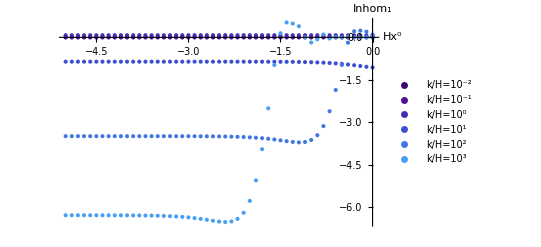

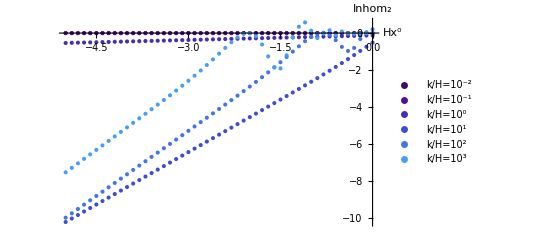

```mathematica
trange=Array[#/10&,51,{-50,0}];
ListPlot[Array[Transpose[{trange,Inhom1List[[All,#]]}]&,6],PlotRange->Full,PlotLegends->{"k/H=10^-2","k/H=10^-1","k/H=10^0","k/H=10^1","k/H=10^2","k/H=10^3"},AxesLabel->{"Hx^0","Inhom_1"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72}]
ListPlot[Array[Transpose[{trange,Inhom2List[[All,#]]}]&,6],PlotRange->Full,PlotLegends->{"k/H=10^-2","k/H=10^-1","k/H=10^0","k/H=10^1","k/H=10^2","k/H=10^3"},AxesLabel->{"Hx^0","Inhom_2"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72}]
```

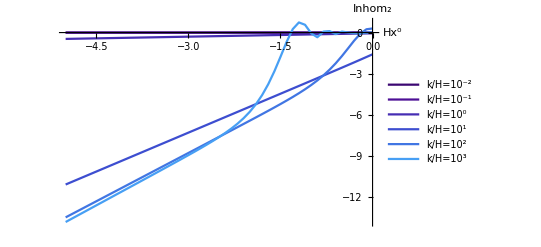

```mathematica
ListPlot[Array[Transpose[{trange,Total[{Inhom2List[[All,#]],Inhom1List[[All,#]]}]}]&,6],PlotRange->Full,PlotLegends->{"k/H=10^-2","k/H=10^-1","k/H=10^0","k/H=10^1","k/H=10^2","k/H=10^3"},AxesLabel->{"Hx^0","Inhom_2"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72},Joined->True]
```

We observe, that the inhomogeneities are converging to zero at late times, almost independent of the modes. To get a better picture, we consider the inhomogeneities at t = 0 for different modes in the following:

```mathematica
Inhom1at0=Array[Inhom1[0,10^(#),1]&,201,{-3,3}];
Inhom2at0=Array[Inhom2[0,10^(#),1]&,201,{-3,3}];
krange=Array[10^(#)&,201,{-3,3}];
```

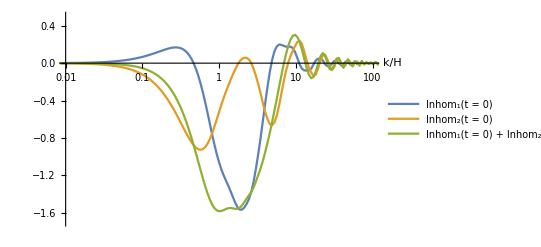

```mathematica
ListLogLinearPlot[{Transpose[{krange,Inhom1at0}],Transpose[{krange,Inhom2at0}],Transpose[{krange,Total[{Inhom1at0,Inhom2at0}]}]},PlotRange->{{0.01,100},{-1.7,0.5}},Joined->True,PlotLegends->{"Inhom_1(t = 0)", "Inhom_2(t = 0)" , "Inhom_1(t = 0) + Inhom_2(t = 0)"},AxesLabel->{"k/H"}]
```

What about the inhomogeneities at -∞? To get a glimpse, we consider a large negative value of time

```mathematica
Inhom1[,1,1]
```

-1.0639

```mathematica
Inhom1atneginfty=Array[Inhom1[-5,10^(#),1]&,201,{-3,3}];
Inhom2atneginfty=Array[Inhom2[-5,10^(#),1]&,201,{-3,3}];
```

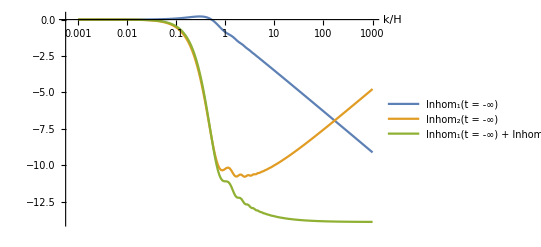

```mathematica
ListLogLinearPlot[{Transpose[{krange,Inhom1atneginfty}],Transpose[{krange,Inhom2atneginfty}],Transpose[{krange,Total[{Inhom1atneginfty,Inhom2atneginfty}]}]},PlotRange->Full,Joined->True,PlotLegends->{"Inhom_1(t = -∞)", "Inhom_2(t = -∞)" , "Inhom_1(t = -∞) + Inhom_2(t = -∞)"},AxesLabel->{"k/H"}]
```

Next, I want to solve the differential equation numerically and show, that the deviation of GFT and GR is indeed encoded in the inhomogeneities, which go to zero at late times for non-Planckian modes.

```mathematica
Subscript[δϕ, GFT,pre][k_,H_,c_]:=NDSolve[{f''[x]+Exp[4*H*x]*k^2*f[x]==c*(-3*H*ϕ̄[x,H]+2*OverBar[dϕ][H] )*(-3 √2 ⅇ^(-(3 H x)/2) H (H/k)^(3/4) BesselJ[3/4,(√(ⅇ^(4 H x)) k)/(2 H)] Gamma[7/4]+√2 ⅇ^(-(3 H x)/2) √(ⅇ^(4 H x)) (H/k)^(3/4) k (BesselJ[-1/4,(√(ⅇ^(4 H x)) k)/(2 H)]-BesselJ[7/4,(√(ⅇ^(4 H x)) k)/(2 H)]) Gamma[7/4]),f[-5]==1, f'[-5]==0},f[x],{x,-5,0}]
Subscript[δϕ, GFT][x_,k_,H_,c_]:=f[x]/.Subscript[δϕ, GFT,pre][k,H,c]
```

For c = 0.01, we plot in the following the matter perturbations of GFT and GR for H  = 1.

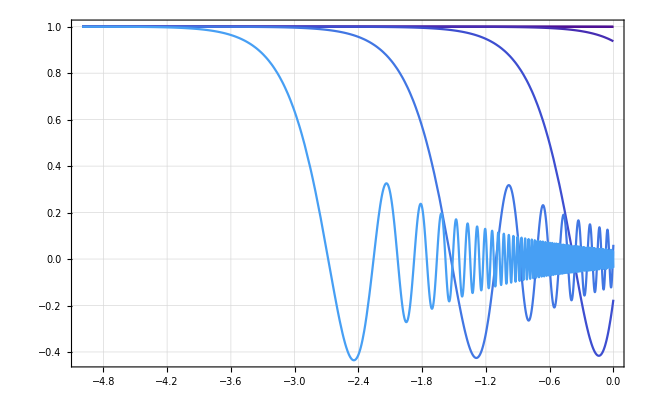

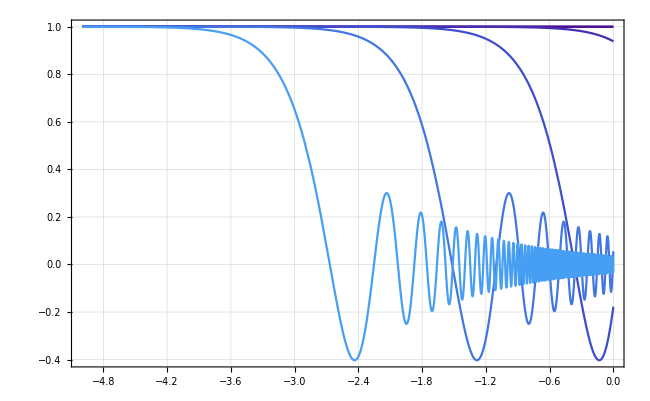

```mathematica
matterpertGFT=Plot[Evaluate@Table[Subscript[δϕ, GFT][x,10^(n),1,0.01],{n,-2,3}],{x,-5,0},Frame->True,GridLines->Automatic ,FrameLabel->{{Style[MaTeX["\delta\phi_{\mathrm{GFT}}", Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72},PlotRange->Full,ImageSize->650,FrameTicksStyle->Directive[FontSize->16]]
matterpertGR=Plot[Evaluate@Table[Subscript[δϕ, GR][x,10^(n),1],{n,-2,3}],{x,-5,0},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\delta\phi_{\mathrm{GR}}", Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72},PlotRange->Full,ImageSize->650,FrameTicksStyle->Directive[FontSize->16]]
Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/matter_pert_GFT.pdf",matterpertGFT];
Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/matter_pert_GR.pdf",matterpertGR];
```

### Plotting the source term J_ϕ

```mathematica
Clear[ϕ̄,OverBar[dϕ]]
```

Clear::ssym: ϕ̄ is not a symbol or a string.

Clear::ssym: OverBar[dϕ] is not a symbol or a string.

```mathematica
ϕ̄[x_,x0_,H_,M_]:=-Sqrt[8/3]*M+Sqrt[6]*M*H*(x-x0);
OverBar[dϕ][H_,M_]:=Sqrt[6]*M*H;
Subscript[J, ϕ][x_,x0_,k_,H_,M_,c_]:=((Exp[2*H*(x-x0)]*k)/M)*c*OverBar[dϕ][x,H,M]*(-3/Sqrt[6]ϕ̄[x,x0,H,M]+2M)*Gamma[7/4]*((4H)/k)^(3/4)*Exp[-3/2 H*(x-x0)]*BesselJ[7/4,(Exp[2*H*(x-x0)] k)/(2 H)];
```

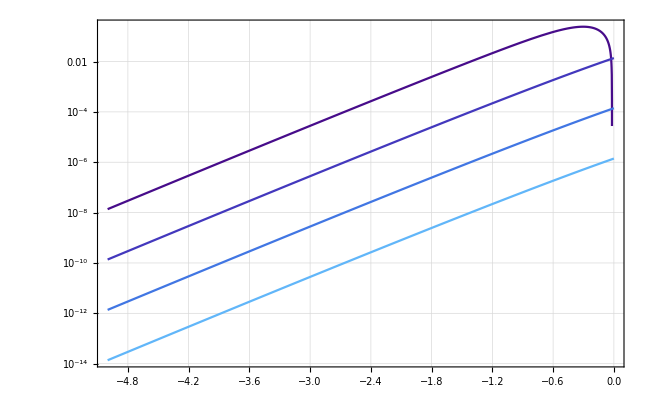

```mathematica
ϕsourceplot = LogPlot[Evaluate@Table[Subscript[J, ϕ][x,0,10^(-n),1,1,0.01],{n,-1,2}],{x,-5,0},Frame->True,GridLines->Automatic ,FrameLabel->{{Style[MaTeX["J_{\phi}", Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.2,0.4,0.6,0.8},PlotRange->Full,ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotLegends->{MaTeX["k/M_{\mathrm{Pl}} = 10^{1}",Magnification->2],MaTeX["k/M_{\mathrm{Pl}} = 10^{0}",Magnification->2],MaTeX["k/M_{\mathrm{Pl}} = 10^{-1}",Magnification->2],MaTeX["k/M_{\mathrm{Pl}} = 10^{-2}",Magnification->2]}]
Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/phi_source.pdf",ϕsourceplot];
```

Change in H leads to shift in the curves.

Next, we consider different values of c for k/H = 10^3 and H = 1, where clearly, larger values of c lead to stronger deviations.

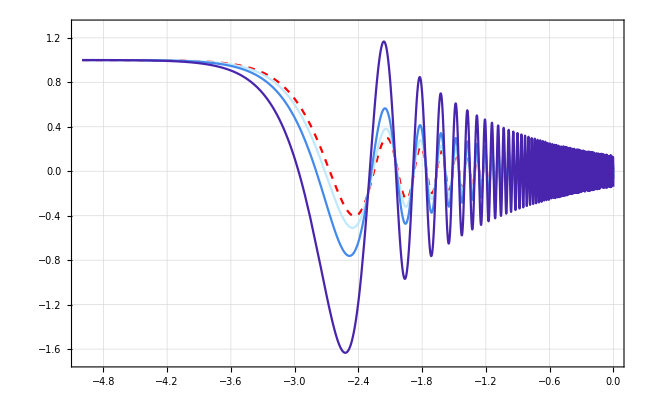

```mathematica
matterpertc = Show[{Plot[Subscript[δϕ, GR][x,10^(3),1],{x,-5,0},PlotStyle->{Red,Dashed},PlotRange->{{-5,0},{-1.7,1.3}},PlotLegends->{MaTeX["\mathrm{GR}",Magnification->2]},LabelStyle->Directive[FontSize->16]],Plot[Evaluate@Table[Subscript[δϕ, GFT][x,10^(3),1,10^(n/2)],{n,-3,-1}],{x,-5,0},PlotRange->Full,PlotStyle->ColorData["DeepSeaColors"]/@{0.99,0.66,0.33},PlotLegends->{MaTeX["c_1^{\mathrm{GR}} = 10^{-1.5}",Magnification->2], MaTeX["c_1^{\mathrm{GR}} = 10^{-1}",Magnification->2], MaTeX["c_1^{\mathrm{GR}} = 10^{-0.5}",Magnification->2]},LabelStyle->Directive[FontSize->16]]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\delta\phi",Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0", Magnification->2],FontSize->16],}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16] ]
Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/matter_pert_c.pdf",matterpertc];
```

What happens for different values of H? Let’s visualize for different fixed modes

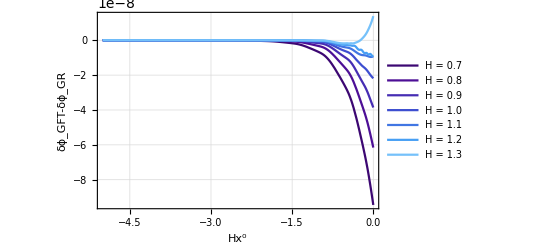

```mathematica
Plot[Evaluate@Table[Subscript[δϕ, GFT][x,10^(-3),1+0.1*n,0.01]-Subscript[δϕ, GR][x,10^(-3),1+0.1*n],{n,-3,3}],{x,-5,0},PlotLegends->{"H = 0.7","H = 0.8", "H = 0.9", "H = 1.0", "H = 1.1", "H = 1.2", "H = 1.3" },Frame->True,GridLines->Automatic ,FrameLabel->{"Hx^0","δϕ_GFT-δϕ_GR"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72, 0.84},PlotRange->Full]
```

```mathematica
Plot[Evaluate@Table[Subscript[δϕ, GFT][x,10^(0),1+0.1*n,0.01]-Subscript[δϕ, GR][x,10^(0),1+0.1*n],{n,-3,3}],{x,-5,0},PlotLegends->{"H = 0.7","H = 0.8", "H = 0.9", "H = 1.0", "H = 1.1", "H = 1.2", "H = 1.3" },Frame->True,GridLines->Automatic ,FrameLabel->{"Hx^0","δϕ_GFT-δϕ_GR"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72, 0.84},PlotRange->Full]
```

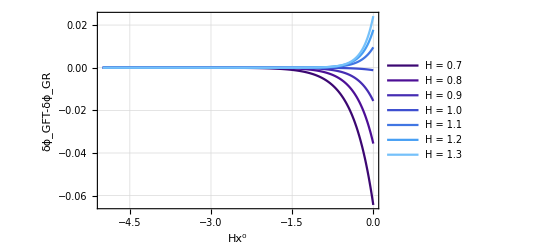

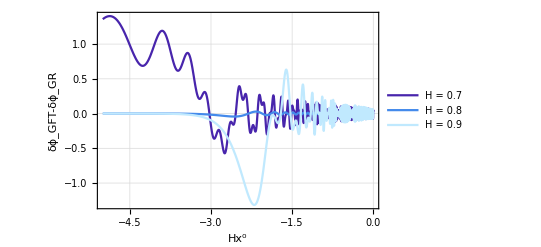

```mathematica
Plot[Evaluate@Table[Subscript[δϕ, GFT][x,10^(3),1+0.1*n,0.01]-Subscript[δϕ, GR][x,10^(3),1+0.5*n],{n,-1,1}],{x,-5,0},PlotLegends->{"H = 0.7","H = 0.8", "H = 0.9", "H = 1.0", "H = 1.1", "H = 1.2", "H = 1.3" },Frame->True,GridLines->Automatic ,FrameLabel->{"Hx^0","δϕ_GFT-δϕ_GR"},PlotStyle->ColorData["DeepSeaColors"]/@{0.33,0.66,0.99},PlotRange->Full]
```

While the GR solution depends solely on the product x^0*H, such that changes in H correspond to a re-scaling, the GFT solution is more sensitive to H as it partially controls the inhomogeneity of the differential equation.

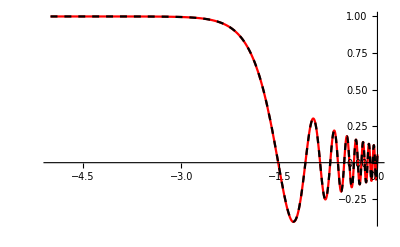

```mathematica
Show[Plot[Evaluate@Table[Subscript[δϕ, GFT][x,10^(2),1,10^(n)],{n,-3,-3}],{x,-5,0},PlotStyle->Red], Plot[Subscript[δϕ, GR][x,10^(2),1],{x,-5,0},PlotStyle->{Dashed,Black}]]
```

```mathematica
diffδϕ=Table[((Subscript[δϕ, GFT][x,krange[[i]],1,0.01]-Subscript[δϕ, GR][x,krange[[i]],1])/.x->t)[[1]],{t,-5,0},{i,1,201}];
```

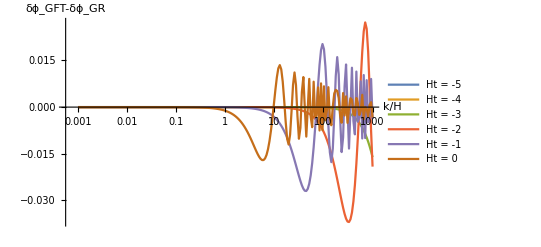

```mathematica
ListLogLinearPlot[Array[Transpose[{krange,diffδϕ[[#]]}]&,6],PlotLegends->{"Ht = -5", "Ht = -4", "Ht = -3", "Ht = -2", "Ht = -1","Ht = 0"},AxesLabel->{"k/H","δϕ_GFT-δϕ_GR"},PlotRange->Full,Joined->True]
```

## Analytical comparison of curvature perturbations

```mathematica
Subscript[R, GR][x_,k_,H_,M_,c_]:=(-c/3+1/Sqrt[6])*BesselJ[0,(√(ⅇ^(4 H x)) k)/(2 H)];
```

The structure of δϕ and R is quite similar, suggesting that the constant c, encoding the relative size of δV and δϕ initial conditions, is important for the matching. We solve in the following the R_GFT-equation numerically and compare the solutions for different c.

```mathematica
Subscript[R, GFT,pre][k_,H_,M_,c_]:=NDSolve[{f''[x]+Exp[4*H*x]*k^2*f[x]==-c(H+(ϕ̄[x,0,H,M])/(2 OverBar[dϕ][H,M]))*(-3 √2 ⅇ^(-(3 H x)/2) H (H/k)^(3/4) BesselJ[3/4,(√(ⅇ^(4 H x)) k)/(2 H)] Gamma[7/4]+√2 ⅇ^(-(3 H x)/2) √(ⅇ^(4 H x)) (H/k)^(3/4) k (BesselJ[-1/4,(√(ⅇ^(4 H x)) k)/(2 H)]-BesselJ[7/4,(√(ⅇ^(4 H x)) k)/(2 H)]) Gamma[7/4]),f[-5]==-c/3+1/Sqrt[6],f'[-5]==0},f[x],{x,-5,0}];
Subscript[R, GFT][t_,k_,H_,M_,c_]:=(f[x]/.Subscript[R, GFT,pre][k,H,M,c]/.x->t)[[1]];
reldiffR[t_,k_,H_,c_]:=Abs[Subscript[R, GFT][t,k,H,c]-Subscript[R, GR][t,k,H,c]]/Subscript[R, GR][t,k,H,c]
ΔR[x_,k_,H_,M_,c_]:=Subscript[R, GFT][x,k,H,M,c]-Subscript[R, GR][x,k,H,M,c]
```

### Plotting the curvature-like perturbations

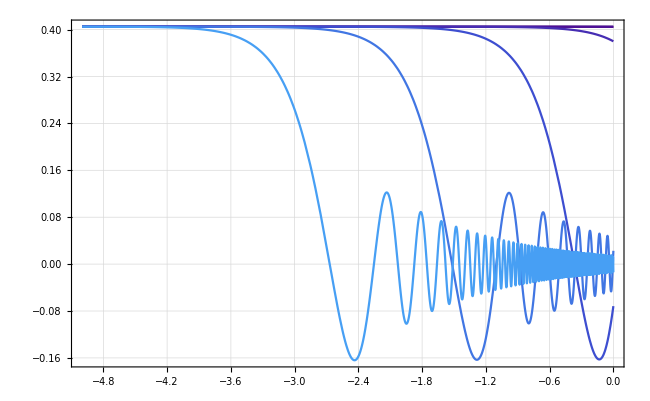

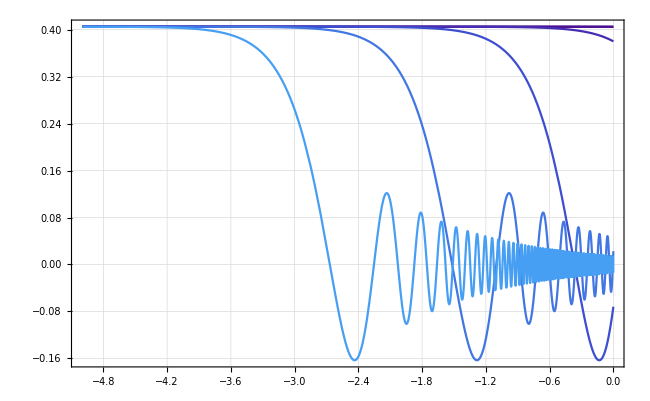

```mathematica
RpertGFT=Plot[Evaluate@Table[Subscript[R, GFT][x,10^(n),1,1,0.01],{n,-2,3}],{x,-5,0},Frame->True,GridLines->Automatic ,FrameLabel->{{Style[MaTeX["\Tilde{\mathcal{R}}_{\mathrm{GFT}}",Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72},PlotRange->Full,ImageSize->650,FrameTicksStyle->Directive[FontSize->16]]
RpertGR=Plot[Evaluate@Table[Subscript[R, GR][x,10^(n),1,1,0.01],{n,-2,3}],{x,-5,0},Frame->True,GridLines->Automatic ,FrameLabel->{{Style[MaTeX["\Tilde{\mathcal{R}}_{\mathrm{GR}}",Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72},PlotRange->Full,ImageSize->650,FrameTicksStyle->Directive[FontSize->16]]
(*Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/R_pert_GFT.pdf",RpertGFT];
Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/R_pert_GR.pdf",RpertGR];
```

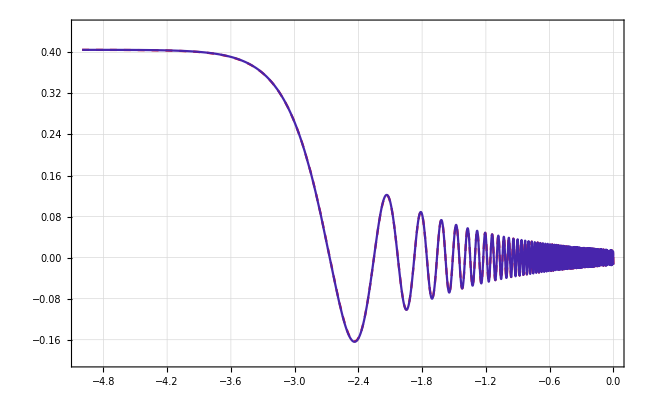

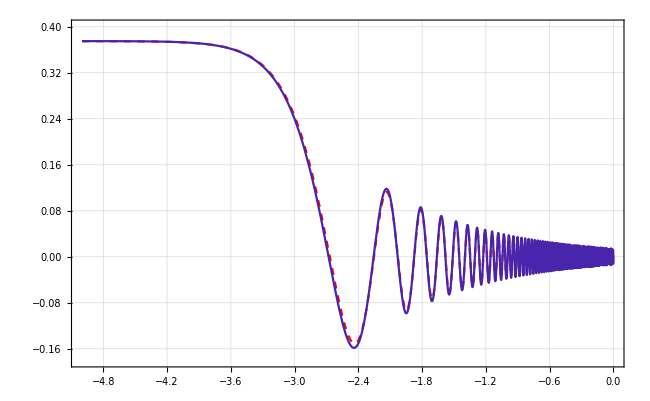

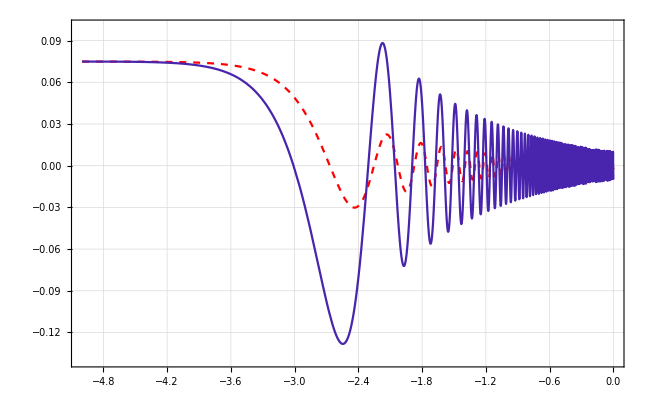

```mathematica
Rpertc1=Show[{Plot[Subscript[R, GR][x,10^(3),1,0.01],{x,-5,0},PlotStyle->{Red,Dashed},PlotRange->{{-5,0},{-0.2,0.45}}],Plot[Evaluate@Table[Subscript[R, GFT][x,10^(3),1,10^(n)],{n,-2,-2}],{x,-5,0},PlotRange->Full,PlotStyle->{ColorData["DeepSeaColors"]/@{0.33}}]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\Tilde{\mathcal{R}}",Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],Style[MaTeX["c_1^{\mathrm{GR}} = 10^{-2}",Magnification->2],FontSize->16]}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16] ]
Rpertc2=Show[{Plot[Subscript[R, GR][x,10^(3),1,0.1],{x,-5,0},PlotStyle->{Red,Dashed},PlotRange->{{-5,0},{-0.18,0.4}}],Plot[Evaluate@Table[Subscript[R, GFT][x,10^(3),1,10^(n)],{n,-1,-1}],{x,-5,0},PlotRange->Full,PlotStyle->{ColorData["DeepSeaColors"]/@{0.99,0.66,0.33},Opacity[0.1]}]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\Tilde{\mathcal{R}}",Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],Style[MaTeX["c_1^{\mathrm{GR}} = 10^{-1}",Magnification->2],FontSize->16]}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16] ]
Rpertc3=Show[{Plot[Subscript[R, GR][x,10^(3),1,1],{x,-5,0},PlotStyle->{Red,Dashed},PlotRange->{{-5,0},{-0.14,0.1}}],Plot[Evaluate@Table[Subscript[R, GFT][x,10^(3),1,10^(n)],{n,0,0}],{x,-5,0},PlotRange->Full,PlotStyle->{ColorData["DeepSeaColors"]/@{0.33}}]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\Tilde{\mathcal{R}}",Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],Style[MaTeX["c_1^{\mathrm{GR}} = 10^{0}",Magnification->2],FontSize->16]}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16] ]
Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/R_pert_c1.pdf",Rpertc1];
Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/R_pert_c2.pdf",Rpertc2];
Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/R_pert_c3.pdf",Rpertc3];
```

### Plotting the source term J_R

```mathematica
ϕ̄[x_,x0_,H_,M_]:=-Sqrt[8/3]*M+Sqrt[6]*M*H*(x-x0);
OverBar[dϕ][x_,H_,M_]:=Sqrt[6]*M*H;
Subscript[J, R][x_,x0_,k_,H_,M_,c_]:=((Exp[2*H*(x-x0)]*k)/M)*c*OverBar[dϕ][x,H,M]*(3/Sqrt[6]-(ϕ̄[x,x0,H,M])/(2*M))*Gamma[7/4]*((4H)/k)^(3/4)*Exp[-3/2 H*(x-x0)]*BesselJ[7/4,(Exp[2*H*(x-x0)] k)/(2 H)];
Subscript[J, R,corr][x_,x0_,k_,H_,M_,c_]:=-((Exp[2*H*(x-x0)]*k)/M)*c*OverBar[dϕ][x,H,M]*(3/Sqrt[6]-(ϕ̄[x,x0,H,M])/(2*M))*Gamma[7/4]*((4H)/k)^(3/4)*Exp[-3/2 H*(x-x0)]*BesselJ[7/4,(Exp[2*H*(x-x0)] k)/(2 H)];
```

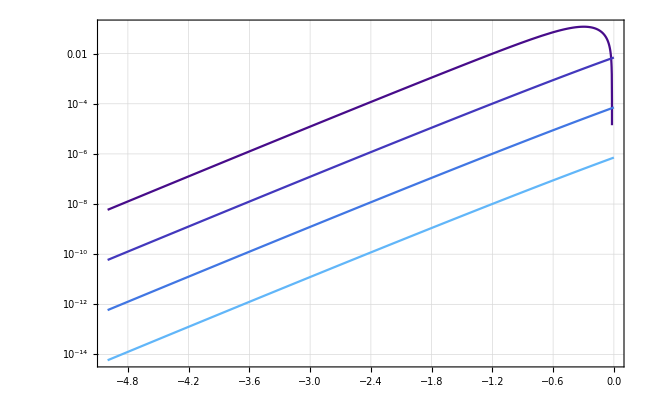

```mathematica
Rsourceplot = LogPlot[Evaluate@Table[Subscript[J, R][x,10^(-n),1,1,0.01],{n,-1,2}],{x,-5,0},Frame->True,GridLines->Automatic ,FrameLabel->{{Style[MaTeX["J_{\mathcal{R}}", Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.2,0.4,0.6,0.8},PlotRange->Full,ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotLegends->{MaTeX["k/M_{\mathrm{Pl}} = 10^{1}",Magnification->2],MaTeX["k/M_{\mathrm{Pl}} = 10^{0}",Magnification->2],MaTeX["k/M_{\mathrm{Pl}} = 10^{-1}",Magnification->2],MaTeX["k/M_{\mathrm{Pl}} = 10^{-2}",Magnification->2]}]
Export["/home/jercheal/Documents/Physics/Articles/GFT perturbations/plots/R_source.pdf",Rsourceplot];
```

Combining the two plots into one:

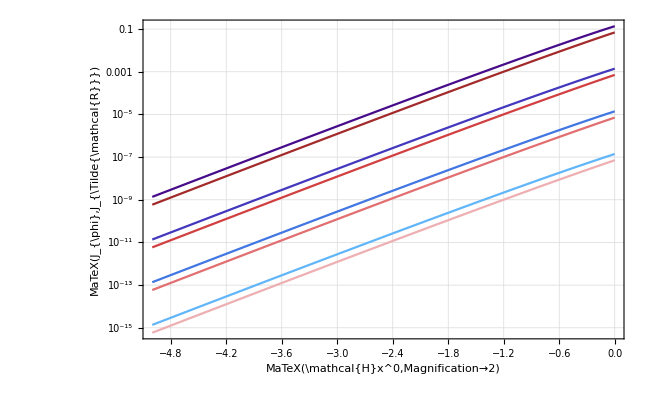

```mathematica
p1=LogPlot[Evaluate@Table[Subscript[J, ϕ][x,0,10^(-n),1,1,0.1],{n,0,3}],{x,-5,0},PlotStyle->ColorData["DeepSeaColors"]/@{0.2,0.4,0.6,0.8},PlotRange->All];
p2=LogPlot[Evaluate@Table[Subscript[J, R][x,0,10^(-n),1,1,0.1],{n,0,3}],{x,-5,0},PlotStyle->ColorData["CherryTones"]/@{0.2,0.4,0.6,0.8}];
sourceplot=Show[{p1,p2},Frame->True,GridLines->Automatic ,FrameLabel->{{Style[MaTeX["J_{\phi},J_{\Tilde{\mathcal{R}}}"],Magnification->2],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotRange->All,ImageSize->650,FrameTicksStyle->Directive[FontSize->16]]
Export["/ssd/ri47hud/Projects/Cosmological Perturbations/plots/source.pdf",sourceplot];
```

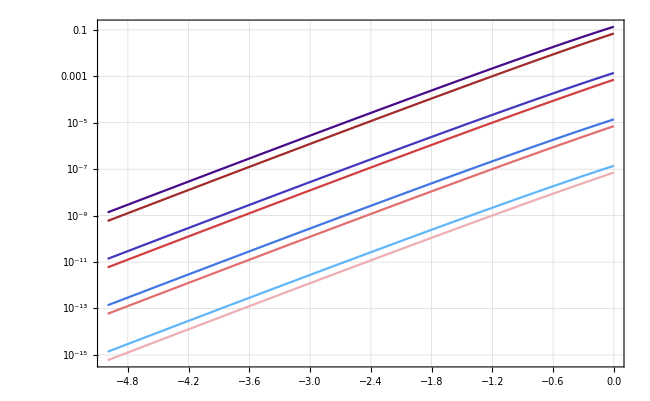

```mathematica
p1=LogPlot[Evaluate@Table[Subscript[J, ϕ][x,0,10^(-n),1,1,0.1],{n,0,3}],{x,-5,0},PlotStyle->ColorData["DeepSeaColors"]/@{0.2,0.4,0.6,0.8},PlotRange->All];
p2=LogPlot[Evaluate@Table[Subscript[J, R][x,0,10^(-n),1,1,0.1],{n,0,3}],{x,-5,0},PlotStyle->ColorData["CherryTones"]/@{0.2,0.4,0.6,0.8}];
sourceplot=Show[{p1,p2},Frame->True,GridLines->Automatic ,FrameLabel->{{Style[MaTeX["\vert J_{\phi}\vert,\:\vert J_{\Tilde{\mathcal{R}}}\vert"],Magnification->2],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotRange->All,ImageSize->650,FrameTicksStyle->Directive[FontSize->16]]
Export["/ssd/ri47hud/Projects/Cosmological Perturbations/plots/source.pdf",sourceplot];
```

### Sophisticated plot for R

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

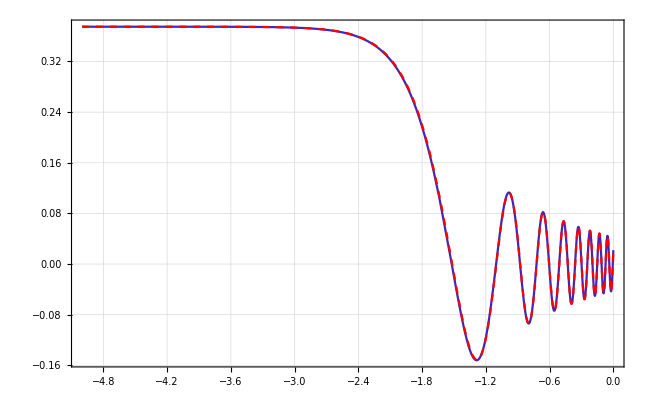

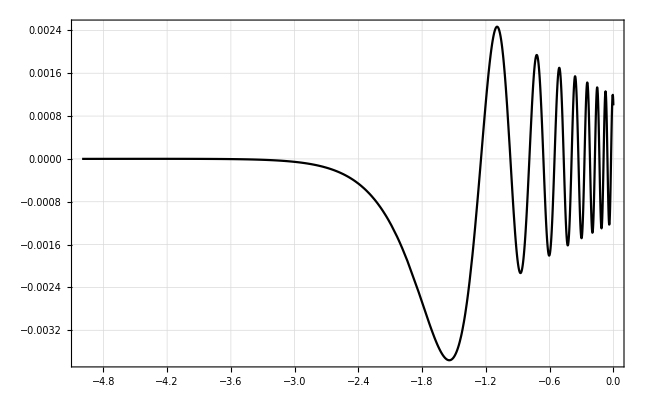

```mathematica
RGFTplot=Show[{Plot[Evaluate@Table[Subscript[R, GFT][x,10^(n),1,1,0.1],{n,2,2}],{x,-5,0},Frame->True,GridLines->Automatic ,FrameLabel->{{Style[MaTeX["\Tilde{\mathcal{R}}",Magnification->2],FontSize->16],},{,}},PlotStyle->{ColorData["DeepSeaColors"]/@{0.33}},PlotRange->Full,FrameTicksStyle->Directive[FontSize->16]],Plot[Evaluate@Table[Subscript[R, GR][x,10^(n),1,1,0.1],{n,2,2}],{x,-5,0},Frame->True,GridLines->Automatic ,FrameLabel->{{Style[MaTeX["\Tilde{\mathcal{R}}",Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotStyle->{Red,Dashed},PlotRange->Full,FrameTicksStyle->Directive[FontSize->16]]}]
DeltaRplot=Plot[Evaluate@Table[ΔR[x,10^(n),1,1,0.1],{n,2,2}],{x,-5,0},PlotStyle->{Black},Frame->True,GridLines->Automatic ,FrameLabel->{{Style[MaTeX["\Delta\Tilde{\mathcal{R}}",Magnification->2],FontSize->16],},{Style[MaTeX["\mathcal{H}x^0",Magnification->2],FontSize->16],}},PlotRange->Full,FrameTicksStyle->Directive[FontSize->16],PlotLegends->{""},ImageSize->650]

plotGrid[{{RGFTplot},{DeltaRplot}},650,800,ImagePadding->120]
```

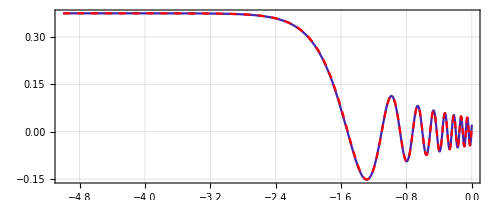

```mathematica
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

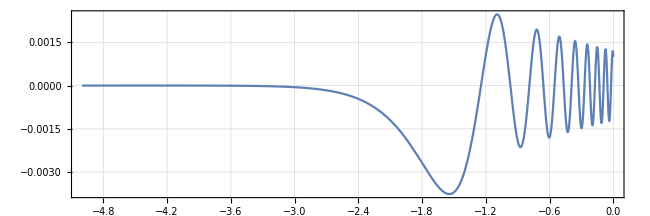

```mathematica
Graphics[{{Inset[Show[RGFTplot,ImagePadding->{{100,10},{0,0}},AspectRatio->Full,PlotRange->Full]]},{Inset[Show[DeltaRplot,ImagePadding->{{0,0},{0,0}},AspectRatio->1/3,PlotRange->Full]]}}]
```

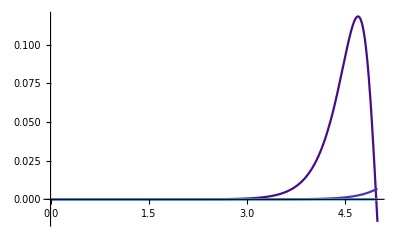

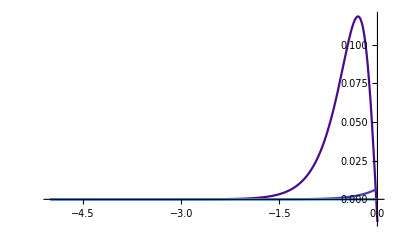

```mathematica
Plot[Evaluate@Table[Subscript[J, R][x,5,10^(-n),1,1,0.01],{n,-1,2}],{x,0,5},PlotStyle->ColorData["DeepSeaColors"]/@{0.2,0.4,0.6,0.8},PlotRange->All]
Plot[Evaluate@Table[Subscript[J, R][x,0,10^(-n),1,1,0.01],{n,-1,2}],{x,-5,0},PlotStyle->ColorData["DeepSeaColors"]/@{0.2,0.4,0.6,0.8},PlotRange->All]
```

Let’s consider the H-dependence for fixed c =  0.01 and for three different exemplary values of k/H.

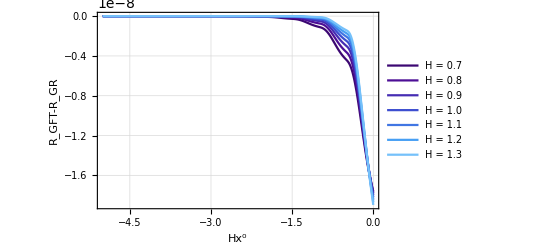

```mathematica
Plot[Evaluate@Table[Subscript[R, GFT][x,10^(-3),1+0.1*n,0.01]-Subscript[R, GR][x,10^(-3),1+0.1*n,0.01],{n,-3,3}],{x,-5,0},PlotLegends->{"H = 0.7","H = 0.8", "H = 0.9", "H = 1.0", "H = 1.1", "H = 1.2", "H = 1.3" },Frame->True,GridLines->Automatic ,FrameLabel->{"Hx^0","R_GFT-R_GR"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72, 0.84},PlotRange->Full]
```

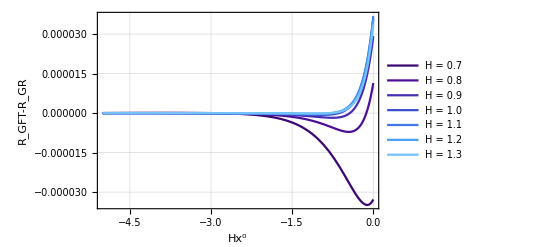

```mathematica
Plot[Evaluate@Table[Subscript[R, GFT][x,10^(0),1+0.1*n,0.01]-Subscript[R, GR][x,10^(0),1+0.1*n,0.01],{n,-3,3}],{x,-5,0},PlotLegends->{"H = 0.7","H = 0.8", "H = 0.9", "H = 1.0", "H = 1.1", "H = 1.2", "H = 1.3" },Frame->True,GridLines->Automatic ,FrameLabel->{"Hx^0","R_GFT-R_GR"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72, 0.84},PlotRange->Full]
```

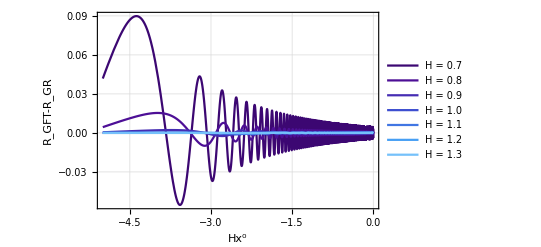

```mathematica
Plot[Evaluate@Table[Subscript[R, GFT][x,10^(3),1+0.1*n,0.01]-Subscript[R, GR][x,10^(3),1+0.1*n,0.01],{n,-3,3}],{x,-5,0},PlotLegends->{"H = 0.7","H = 0.8", "H = 0.9", "H = 1.0", "H = 1.1", "H = 1.2", "H = 1.3" },Frame->True,GridLines->Automatic ,FrameLabel->{"Hx^0","R_GFT-R_GR"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72, 0.84},PlotRange->Full]
```

```mathematica
+
```

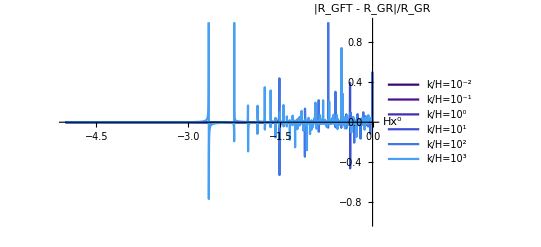

```mathematica
Plot[Evaluate@Table[reldiffR[x,10^(n),1,0.01],{n,-2,3}],{x,-5,0},PlotLegends->{"k/H=10^-2","k/H=10^-1","k/H=10^0","k/H=10^1","k/H=10^2","k/H=10^3"},AxesLabel->{"Hx^0","|R_GFT - R_GR|/R_GR"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72},PlotRange->{{-5,0},{-1,1}}]
```

Let’s plot the relative error for fixed mode and for varying ratio c:

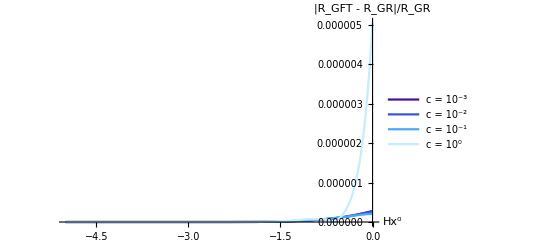

```mathematica
Plot[Evaluate@Table[reldiffR[x,10^(-2),1,10^(n)],{n,-3,0}],{x,-5,0},PlotLegends->{"c = 10^-3" , "c = 10^-2", "c = 10^-1", "c = 10^0" },AxesLabel->{"Hx^0","|R_GFT - R_GR|/R_GR"},PlotStyle->ColorData["DeepSeaColors"]/@{0.25,0.5,0.75,1.0},PlotRange->Full]
```

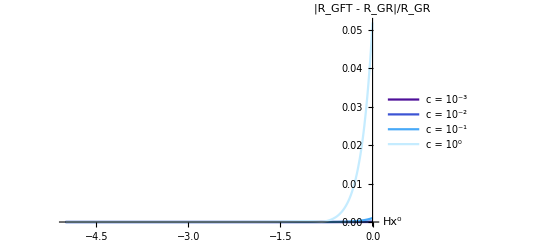

```mathematica
Plot[Evaluate@Table[reldiffR[x,10^(0),1,10^(n)],{n,-3,0}],{x,-5,0},PlotLegends->{"c = 10^-3" , "c = 10^-2", "c = 10^-1", "c = 10^0" },AxesLabel->{"Hx^0","|R_GFT - R_GR|/R_GR"},PlotStyle->ColorData["DeepSeaColors"]/@{0.25,0.5,0.75,1.0},PlotRange->Full]
```

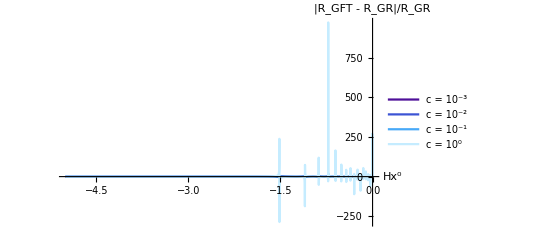

```mathematica
Plot[Evaluate@Table[reldiffR[x,10^(2),1,10^(n)],{n,-3,0}],{x,-5,0},PlotLegends->{"c = 10^-3" , "c = 10^-2", "c = 10^-1", "c = 10^0" },AxesLabel->{"Hx^0","|R_GFT - R_GR|/R_GR"},PlotStyle->ColorData["DeepSeaColors"]/@{0.25,0.5,0.75,1.0},PlotRange->Full]
```

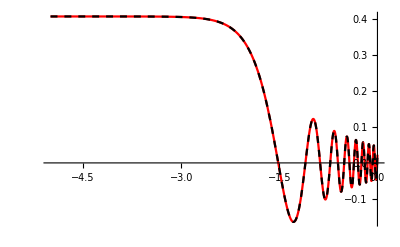

```mathematica
Show[Plot[Evaluate@Table[Subscript[R, GFT][x,10^(2),1,10^(n)],{n,-3,-3}],{x,-5,0},PlotStyle->Red],Plot[Subscript[R, GR][x,10^(2),1,10^(-3)],{x,-5,0},PlotStyle->{Black,Dashed}],PlotRange->Full]
```

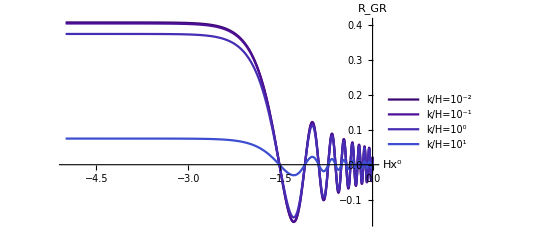

```mathematica
Plot[Evaluate@Table[Subscript[R, GR][x,10^(2),1,10^(n)],{n,-3,0}],{x,-5,0},PlotLegends->{"k/H=10^-2","k/H=10^-1","k/H=10^0","k/H=10^1","k/H=10^2","k/H=10^3"},AxesLabel->{"Hx^0","R_GR"},PlotStyle->ColorData["DeepSeaColors"]/@{0.12,0.24,0.36,0.48,0.6,0.72},PlotRange->Full]
```